找到的最大值点是：1.5708

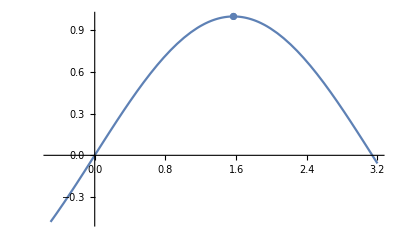

```mathematica
goldensectionMethod[f_,{a_,b_},tol_:0.000001,maxIter_:1000]:=Module[
{ax,bx,cx,dx,iter=0},
cx=a+(2-GoldenRatio)*(b-a);
dx=b-(2-GoldenRatio)*(b-a);
ax=a;
bx=b;
While[Abs[ax-bx]>tol && iter<maxIter,
iter++;
If[f[cx]>f[dx],bx=dx,ax=cx;];
cx=ax+(2-GoldenRatio)*(bx-ax);
dx=bx-(2-GoldenRatio)*(bx-ax);
];
Return[If[iter==maxIter-1,"未达到所需精度或最大迭代次数",cx]];
];
f[x_]=Sin[x];
root=goldensectionMethod[f,{-0.5,3.2}];
Print["找到的最大值点是：",root];
Curve1=Plot[f[x],{x,-0.5,3.2}];
Curve2=ListPlot[{{root,f[root]}}];
Show[Curve1,Curve2]
```